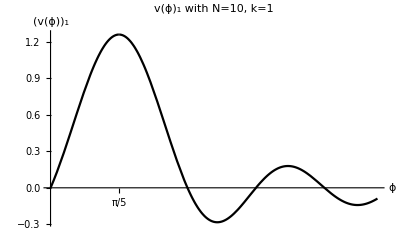

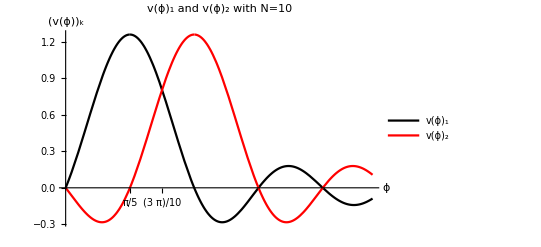

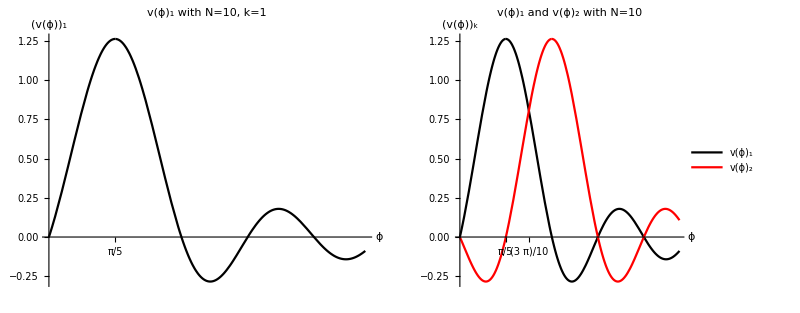

```mathematica
v[k_, t_, n_]:= (2 Pi n)^(-1/2)Sin[n/2(t-(2 Pi k)/n)]/Sin[1/2(t-(2 Pi k)/n)]
plot1 = Plot[{v[1,t,10],Line[{{1,1},{2,2}}]},{t,0,3}, PlotStyle->Black, AxesLabel->{ϕ,Subscript[v[ϕ], 1]}, PlotLabel-> "v(ϕ)_1 with N=10, k=1", Ticks -> {{2Pi/10},None}, ImagePadding->20]
plot2 = Plot[{v[1,t,10],v[2,t,10]},{t,0,3},PlotStyle->{Black,Red},AxesLabel->{ϕ,Subscript[v[ϕ], k]},PlotLabel->"v(ϕ)_1 and v(ϕ)_2 with N=10", Ticks->{{2Pi/10,3Pi/10},None},PlotLegends->Placed[{"v(ϕ)_1", "v(ϕ)_2"},{Right,Top}],ImagePadding->20]
GraphicsRow[{plot1,plot2}]
```

```mathematica
Export["/Users/jamespuleston/Documents/Cambridge/Essay/TunnellingTimesInQuantumMechanics/Mathematica/plot1.pdf",GraphicsRow[{plot1,plot2}]]
```

/Users/jamespuleston/Documents/Cambridge/Essay/TunnellingTimesInQuantumMechanics/Mathematica/plot1.pdf

```mathematica
tz[r_]:=((1-2r^2)Sinh[3Pi Sqrt[1-r^2]]^2+3 Pi/2 Sqrt[1-r^2]Sinh[6Pi Sqrt[1-r^2]])/(3Pi(4r^2(1-r^2)^2+(1-r^2)Sinh[3Pi(1-r^2)]^2))
```

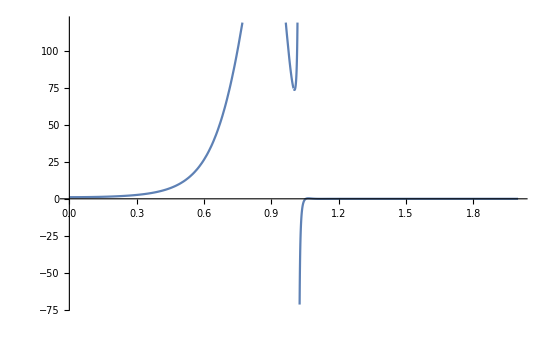

```mathematica
Plot[tz[r],{r,0,2}]
```